## This notebook is for providing the flux of cosmic ray muons at shallow depths. It starts with the parametrization according to ECoMUG. We will use the fit from EcoMug to perform the calculation. EcoMug: An Efficient COsmic MUon Generator for cosmic-ray muon applications. D. Pagano et al., NIM A 1014 (2021) 165732

### Here we setup some parameters. These are for energy loss evaluation. For shallow depth. Simply use the formula E_mu(x) = E_mu(0) - apar * X Now for apar use the value that is average of values at 10 and 100 GeV. The differential spectrum remains the same, but it is simply shifted in this 1 dimensional calculation. x is the depth. Units are as follows Energy in GeV, range in km.w.e, apar in MeV/gm/cm^2, bpar in 10^(-6)/gm/cm^2

```mathematica
Emutab = {10, 100, 1000, 10000};
Rangtab = {0.05,0.41, 2.45, 6.09};
apar ={2.17,2.44, 2.68, 2.93}; 
bbrems ={ 0.7, 1.1, 1.44, 1.62}*10^-6;
bpair ={ 0.7, 1.53, 2.07, 2.27}*10^-6; 
bnucl= {0.5,0.41,0.41,0.46}*10^-6;
bpar= bbrems+bpair+bnucl; 
bice = {1.66,2.51, 3.17, 3.78}*10^-6;
```

### Formula for the ECOMUG fit. The formula arguments are pmu in GeV/c is the momentum of the cosmic muon, and x = Cos(th) is the cosine of the zenith angle. The output is in units of flux per m^2 per second per steradians at the specified angle.

```mathematica
dalt[pmu_, x_]:= Module[{npo, tmp }, npo = Max[0.1, 2.856-0.655Log[pmu]];  tmp =(1600*(pmu + 2.68)^-3.175 * (pmu)^0.279)*x^npo ; Return[tmp]] ;
```

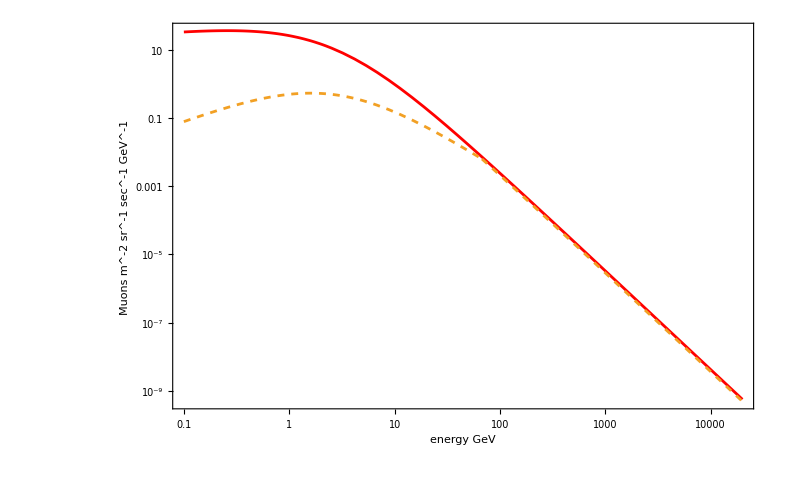

```mathematica
p2 = LogLogPlot[{dalt[emu,1],dalt[emu,0.25]} ,{emu,0.1, 20000}, Frame -> True , LabelStyle -> {Bold, Large, Italic} , FrameLabel -> {"energy GeV", "Muons m^-2 sr^-1 sec^-1 GeV^-1" }, PlotStyle -> {Red, Dashed} ]
```

## This is a one dimensional calculation of the flux at some shallow depth (argument depth is in meters). It uses an average energy loss and computes the flux according to the surface flux for the corresponding surface energy of the muon. The slant depth is calculated according to the polar angle and a flat surface. No accounting for earth’s curvature, multiple scattering, or energy loss fluctuations are done. This calculation is only good for modest depths of a few hundred meters.

```mathematica
DmuShallow2[emu_,x_, depth_]:= Module[{aave,  slantdepth, eloss , esurf, tmp, costh }, 
aave = (apar[[1]]+apar[[2]])/2;  (* This is in MeV/gm/cm^2 *)  
slantdepth = If[x>0, 100*depth/x, 12742000];  (* this is in meters Set maximum to be Earth's diameter *)  
density = 1.0;  (* just use water for now *)  
eloss =aave*density*slantdepth * 10^-3;  (* this is to get it into GeV *)  
(*Print[eloss]; *) 
esurf = emu + eloss;   (* this should be in GeV *)  
costh = x; 
tmp = dalt[esurf, costh]; 
Return[tmp]; 
   ]
```

### Muon spectrum at 200 meters depth for vertical and at 75 degrees.

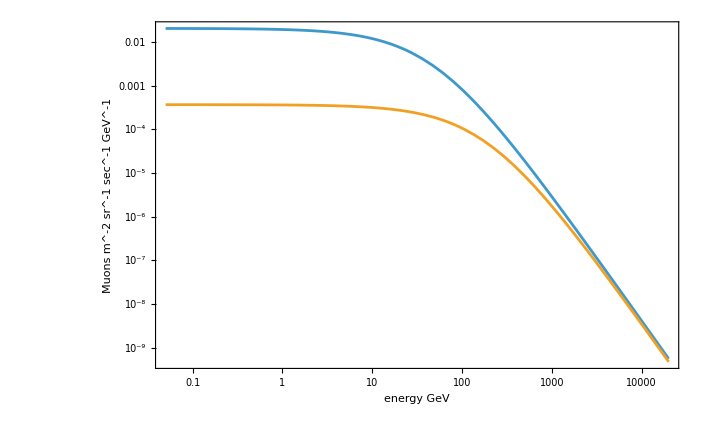

```mathematica
pdeep= LogLogPlot[{DmuShallow2[emu,1. , 200.],  DmuShallow2[emu,0.25, 200.] },{emu,0.05, 20000 }, Frame -> True , LabelStyle -> {Bold, Large, Italic} , FrameLabel -> {"energy GeV", "Muons m^-2 sr^-1 sec^-1 GeV^-1" }]
```

### To calculate intensity on a flat horizontal surface we must integrate over the azimulathal angle which provides a factor of 2 Pi, but we also have to correct for the zenith angle and multiply by Cos(th). We integrate over angle from Cos(th) of 0.1 to 1 and over energy from 1 to 100 GeV. The calculation is in 5 m steps of depth from 1 meters water equivalent to 1000 meters water equivalent. At high depth the calculation is likely to overestimate because we have not included energy loss due to bremsstrahlung.

```mathematica
inten1 =  Table[{jd,2 * Pi* NIntegrate[DmuShallow2[pmu, x,jd]*x, {pmu, 0.05, 1000},{x, 0.1, 1}]} ,  {jd, 1, 1006, 5}]
```

{{1,117.972},{6,70.9961},{11,46.4335},{16,32.8239},{21,24.5295},{26,19.0917},{31,15.3239},{36,12.599},{41,10.56},{46,8.99171},{51,7.75745},{56,6.76726},{61,5.95979},{66,5.29196},{71,4.73282},{76,4.2596},{81,3.85528},{86,3.50688},{91,3.20437},{96,2.93991},{101,2.70727},{106,2.50148},{111,2.31849},{116,2.15501},{121,2.00833},{126,1.8762},{131,1.75672},{136,1.64832},{141,1.54966},{146,1.4596},{151,1.37715},{156,1.30149},{161,1.23187},{166,1.16768},{171,1.10836},{176,1.05342},{181,1.00246},{186,0.955093},{191,0.910992},{196,0.869865},{201,0.831452},{206,0.795521},{211,0.761864},{216,0.730295},{221,0.700646},{226,0.672767},{231,0.64652},{236,0.621782},{241,0.598441},{246,0.576394},{251,0.555549},{256,0.535821},{261,0.517132},{266,0.499411},{271,0.482592},{276,0.466617},{281,0.451428},{286,0.436977},{291,0.423215},{296,0.4101},{301,0.397591},{306,0.38565},{311,0.374245},{316,0.363342},{321,0.352913},{326,0.342931},{331,0.33337},{336,0.324206},{341,0.315419},{346,0.306986},{351,0.29889},{356,0.291112},{361,0.283636},{366,0.276446},{371,0.269528},{376,0.262868},{381,0.256454},{386,0.250273},{391,0.244314},{396,0.238567},{401,0.233021},{406,0.227667},{411,0.222497},{416,0.217502},{421,0.212673},{426,0.208005},{431,0.203489},{436,0.19912},{441,0.19489},{446,0.190794},{451,0.186826},{456,0.182981},{461,0.179254},{466,0.17564},{471,0.172134},{476,0.168733},{481,0.165432},{486,0.162226},{491,0.159114},{496,0.15609},{501,0.153151},{506,0.150295},{511,0.147518},{516,0.144818},{521,0.14219},{526,0.139634},{531,0.137146},{536,0.134724},{541,0.132366},{546,0.130069},{551,0.127831},{556,0.12565},{561,0.123525},{566,0.121453},{571,0.119432},{576,0.117462},{581,0.115539},{586,0.113664},{591,0.111833},{596,0.110047},{601,0.108302},{606,0.106599},{611,0.104935},{616,0.10331},{621,0.101722},{626,0.100171},{631,0.0986543},{636,0.0971718},{641,0.0957223},{646,0.0943048},{651,0.0929184},{656,0.0915622},{661,0.0902353},{666,0.0889369},{671,0.0876661},{676,0.0864222},{681,0.0852044},{686,0.084012},{691,0.0828442},{696,0.0817005},{701,0.0805801},{706,0.0794824},{711,0.0784069},{716,0.0773528},{721,0.0763197},{726,0.075307},{731,0.0743141},{736,0.0733405},{741,0.0723858},{746,0.0714494},{751,0.0705309},{756,0.0696299},{761,0.0687458},{766,0.0678782},{771,0.0670269},{776,0.0661912},{781,0.065371},{786,0.0645657},{791,0.063775},{796,0.0629986},{801,0.0622362},{806,0.0614873},{811,0.0607517},{816,0.060029},{821,0.0593191},{826,0.0586214},{831,0.0579359},{836,0.0572621},{841,0.0565999},{846,0.055949},{851,0.055309},{856,0.0546799},{861,0.0540612},{866,0.0534528},{871,0.0528545},{876,0.0522661},{881,0.0516872},{886,0.0511178},{891,0.0505576},{896,0.0500064},{901,0.0494641},{906,0.0489303},{911,0.0484051},{916,0.0478881},{921,0.0473792},{926,0.0468782},{931,0.046385},{936,0.0458994},{941,0.0454213},{946,0.0449504},{951,0.0444868},{956,0.0440301},{961,0.0435803},{966,0.0431372},{971,0.0427007},{976,0.0422707},{981,0.0418471},{986,0.0414296},{991,0.0410182},{996,0.0406129},{1001,0.0402133},{1006,0.0398196}}

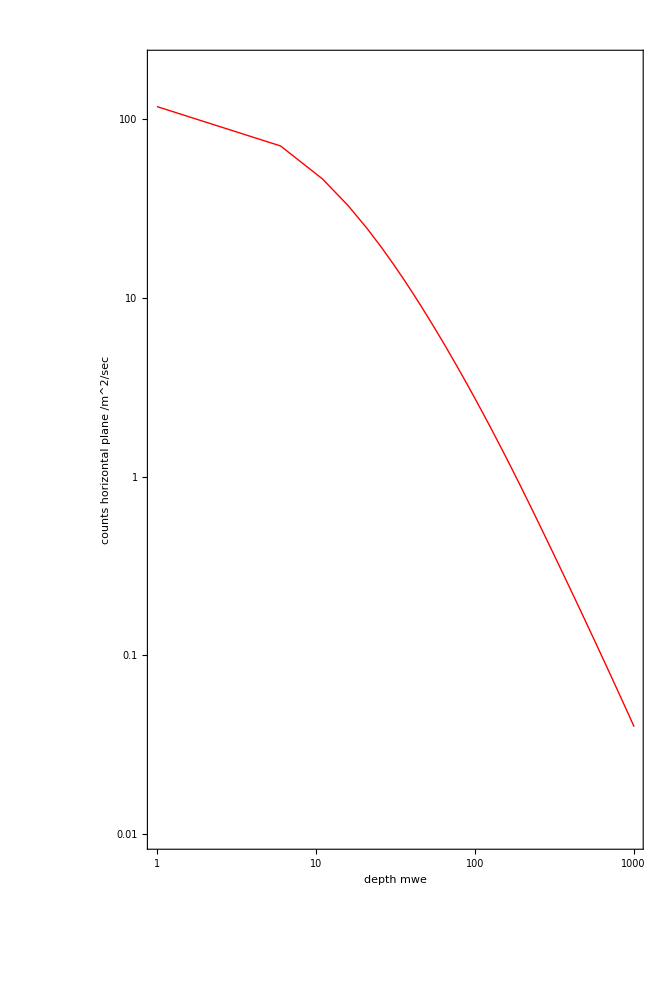

```mathematica
ListLogLogPlot[inten1, Frame -> True, FrameLabel-> {"depth mwe", "counts horizontal plane /m^2/sec"}, Frame -> True,PlotRange -> {{1, 1000}, {10^-2, 200 } }, AspectRatio -> 1.5,FrameStyle-> Bold, LabelStyle-> {Bold, Large, Italic},Joined-> True,PlotStyle -> {Thick, Red}]
```

#### Now we will work on generation of muons from the top surface and side surface at some depth. For this we need to use the appropriate PDFs. We will use the Metropolis algorithm with two dimensions. The idea is to only produce the polar angle and the momentum and provide in a file. The location on the horizontal surface can be generated uniformly. The azimuthal angle can be generated uniformly also if there is no effect of magnetic field. The PDF needs to have limits using the UnitStep function to make sure generation is between 1 - 100 GeV and polar angle Cos(th) of 0 to 1. We will use x = cos(th) for generation. The correct PDF is the projection of the flux on the horizontal surface.

```mathematica
depth = 188; 
horpdf[pmu_,x_]:= 2 * Pi* DmuShallow2[pmu, x,depth]*x*(UnitStep[x]-UnitStep[x-1])*(UnitStep[pmu-1]-UnitStep[pmu-100]);
```

```mathematica
Ntrials = 250000; 
xmu =  Table[{0,0},{i,Ntrials}]; 
xmu[[1]]={1.,0.999} ;  (* just an initial guess *)  
mypdf[x_]:= horpdf[x[[1]], x[[2]]];  (* we just need a function that is proportional to the TARGET PDF pass the parameter as a 2vector*) 
For[i=1,i< Ntrials, i++, (* go through all trials *)  
 xnew = xmu[[i]]+{(RandomReal[] -0.5 )*10. , (RandomReal[] -0.5)*0.1 }  ;  (*get a new number within +- 0.25 of the previous.  Try it with a smaller or larger number *)  
  (*xnew = xg[[i]]+RandomVariate[NormalDistribution[0,1]]*0.05; *)(* Try it this way. It does not matter what the initial PDF is  *)  
If [ RandomReal[]<Min[1,mypdf[xnew]/mypdf[xmu[[i]]]],
xmu[[i+1]]=xnew, xmu[[i+1]]=xmu[[i]]
]
]
```

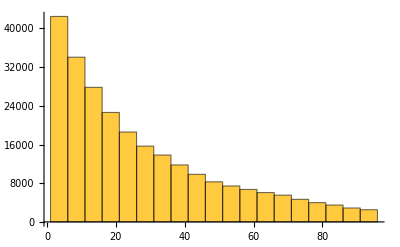

```mathematica
Histogram[Flatten[First[#]&/@xmu ],{1, 100, 5}  ]
```

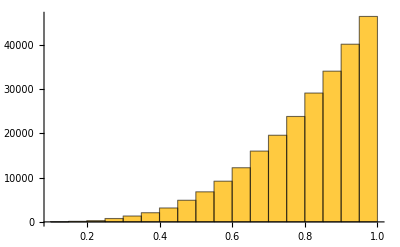

```mathematica
Histogram[Flatten[Last[#]&/@xmu ] ]
```

```mathematica
Now we do this for the vertical plane.  Or muons from the side. No muons should come below the horizon or x = 0.  This is a little bit tricky for the azimuthal angle. For depth use  the midpoint of the sides.   And so,  we generate the position on the vertical plane uniformly (although the flux should drop from top to bottom, we will assume that the drop is small) .  Then we generate the azimuthal according to   cos(phi) with respect to the normal to the plane.  Notice that the polar angle dependence is in x = cos(th).      There is only 1 power of sin(th) since the generation is in x and not in theta.   This will provide the projection of the flux on the vertical surface.
```

```mathematica
depth = 198;  
vertpdf[pmu_,x_] :=  2*DmuShallow2[pmu, x,depth]*Sqrt[1-x^2]*(UnitStep[x]-UnitStep[x-1])*(UnitStep[pmu-1]-UnitStep[pmu-100]);
```

```mathematica
Ntrials = 250000; 
xmu =  Table[{0,0},{i,Ntrials}]; 
xmu[[1]]={1.,0.999} ;  (* just an initial guess *)  
mypdf[x_]:= vertpdf[x[[1]], x[[2]]];  (* we just need a function that is proportional to the TARGET PDF   pass the parameter as a 2vector*) 
For[i=1,i< Ntrials, i++, (* go through all trials *)  
 xnew = xmu[[i]]+{(RandomReal[] -0.5 )*10. , (RandomReal[] -0.5)*0.1 }  ;  (*get a new number within +- 0.25 of the previous.  Try it with a smaller or larger number *)  
  (*xnew = xg[[i]]+RandomVariate[NormalDistribution[0,1]]*0.05; *)(* Try it this way. It does not matter what the initial PDF is  *)  
If[xnew[[2]]>1, xnew[[2]]=1]; 
If [ RandomReal[]<Min[1,mypdf[xnew]/mypdf[xmu[[i]]]],
xmu[[i+1]]=xnew, xmu[[i+1]]=xmu[[i]]
]
]
```

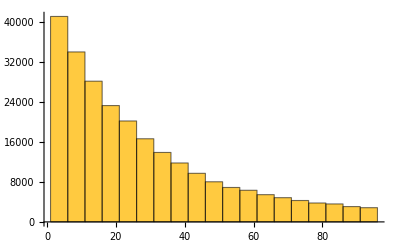

```mathematica
Histogram[Flatten[First[#]&/@xmu ],{1, 100, 5}  ]
```

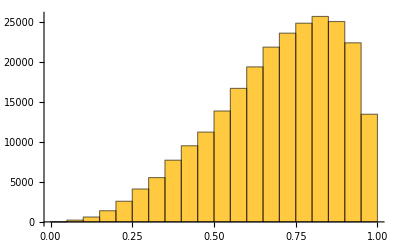

```mathematica
Histogram[Flatten[Last[#]&/@xmu ] ]
```